# Scattering Kernels in 3D

This is code to accompany the book:
A Hitchhiker’s Guide to Multiple Scattering
© 2015 Eugene d’Eon 
www.eugenedeon.com

## Isotropic Scattering

```mathematica
pIsotropic[u_]:=1/(4Pi)
```

### Normalization condition

```mathematica
Integrate[2 Pi pIsotropic[u],{u,-1,1}]
```

1

### Mean-cosine

```mathematica
Integrate[2 Pi pIsotropic[u]u,{u,-1,1}]
```

0

### Legendre expansion coefficients

```mathematica
Integrate[2 Pi (2k+1)pIsotropic[Cos[y]]LegendreP[k,Cos[y]]Sin[y]/.k->0,{y,0,Pi}]
```

1

```mathematica
Integrate[2 Pi (2k+1)pIsotropic[Cos[y]]LegendreP[k,Cos[y]]Sin[y]/.k->1,{y,0,Pi}]
```

0

### sampling

```mathematica
cdf=Integrate[2 Pi pIsotropic[u],{u,-1,x}]
```

(1+x)/2

```mathematica
Solve[cdf==e,x]
```

{{x→-1+2 e}}

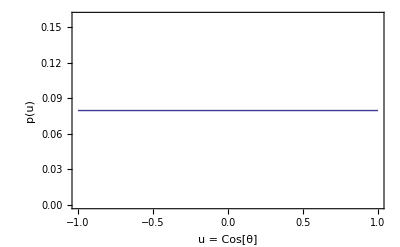

```mathematica
Clear[u];Show[
Plot[pIsotropic[u],{u,-1,1},PlotStyle->Thick]
,Frame->True,
FrameLabel->{{p[u],},{"u = Cos[θ]","Isotropic Scattering"}}]
```

## Linearly-Anisotropic Scattering

```mathematica
pLinaniso[u_,b_]:=1/(4 Pi)(1+b u)
```

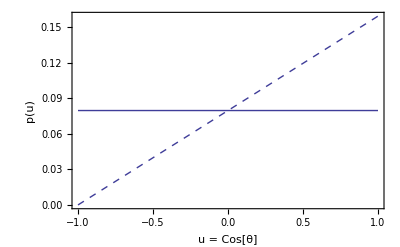

```mathematica
Clear[u];
Show[
Plot[pIsotropic[u],{u,-1,1},PlotStyle->Thick],
Plot[pLinaniso[u,1],{u,-1,1},PlotStyle->Dashed]
,Frame->True,
FrameLabel->{{p[u],},{"u = Cos[θ]","Linearly-Anisotropic Scattering"}}]
```

### Normalization condition

```mathematica
Integrate[2 Pi pLinaniso[u,b],{u,-1,1},Assumptions->b>-1&&b<1]
```

1

### Mean cosine (g)

```mathematica
Integrate[2 Pi pLinaniso[u,b]u,{u,-1,1},Assumptions->b>-1&&b<1]
```

b/3

### Legendre expansion coefficients

```mathematica
Integrate[2Pi(2k+1)pLinaniso[Cos[y],b]LegendreP[k,Cos[y]]Sin[y]/.k->0,{y,0,Pi}]
```

1

```mathematica
Integrate[2Pi(2k+1)pLinaniso[Cos[y],b]LegendreP[k,Cos[y]]Sin[y]/.k->1,{y,0,Pi}]
```

b

### sampling

```mathematica
cdf=Integrate[2 Pi pLinaniso[u,b],{u,-1,x}]
```

1/2-b/4+x/2+(b x^2)/4

```mathematica
Solve[cdf==e,x]
```

{{x→(-1-√(1-2 b+b^2+4 b e))/b},{x→(-1+√(1-2 b+b^2+4 b e))/b}}

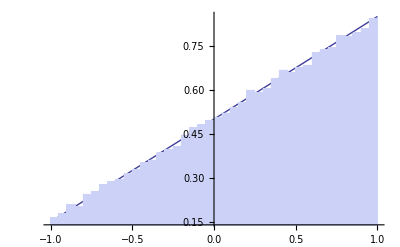

```mathematica
b=0.7;
Show[
Plot[2 Pi pLinaniso[u,b],{u,-1,1}],
Histogram[Map[(-1+√(1-2 b+b^2+4 b #))/b&,Table[RandomReal[],{i,1,100000}]],50,"PDF"]
]
Clear[b];
```

## Rayleigh Scattering

```mathematica
pRayleigh[u_]:=(1+u^2)3/(16 Pi)
```

### Normalization condition

```mathematica
Integrate[2 Pi pRayleigh[u],{u,-1,1},Assumptions->b>-1&&b<1]
```

1

### Mean cosine (g)

```mathematica
Integrate[2 Pi pRayleigh[u]u,{u,-1,1},Assumptions->b>-1&&b<1]
```

0

### Legendre expansion coefficients

```mathematica
Integrate[2Pi(2k+1)pRayleigh[Cos[y]]LegendreP[k,Cos[y]]Sin[y]/.k->0,{y,0,Pi}]
```

1

```mathematica
Integrate[2Pi(2k+1)pRayleigh[Cos[y]]LegendreP[k,Cos[y]]Sin[y]/.k->1,{y,0,Pi}]
```

0

```mathematica
Integrate[2Pi(2k+1)pRayleigh[Cos[y]]LegendreP[k,Cos[y]]Sin[y]/.k->2,{y,0,Pi}]
```

1/2

### sampling

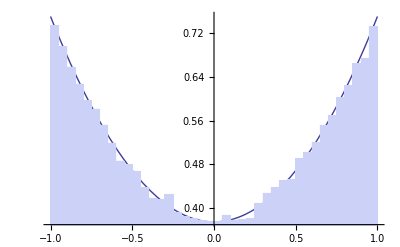

```mathematica
Show[
Plot[2 Pi pRayleigh[u],{u,-1,1}],
Histogram[Map[(1-(2-4 #+√(5+16 (-1+#)#))^(2/3))/(2-4 #+√(5+16 (-1+#) #))^(1/3)&,Table[RandomReal[],{i,1,100000}]],50,"PDF"]
]
Clear[b];
```

## Henyey-greenstein Scattering

```mathematica
Clear[pHG];pHG[dot_,g_]:=1/(4 Pi)(1-g^2)/((1+g^2-2g dot)^(3/2))
```

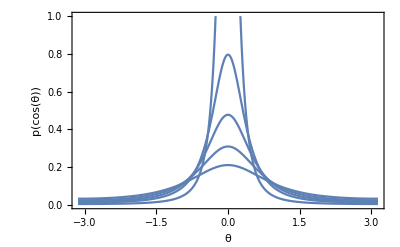

```mathematica
pHGplot=Show[
Plot[pHG[Cos[t],.8],{t,-Pi,Pi},PlotRange->{0,1}],
Plot[pHG[Cos[t],.6],{t,-Pi,Pi},PlotRange->All],
Plot[pHG[Cos[t],.5],{t,-Pi,Pi},PlotRange->All],
Plot[pHG[Cos[t],.4],{t,-Pi,Pi},PlotRange->All],
Plot[pHG[Cos[t],.3],{t,-Pi,Pi},PlotRange->All],
Frame->True,
ImageSize->400,
FrameLabel->{{p[Cos[θ]],},{θ,"Henyey-Greenstein Scattering, g = 0.3, 0.4, 0.5, 0.6, 0.8"}}]
```

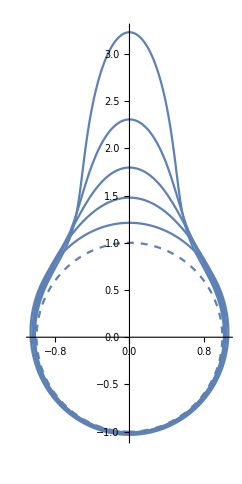

```mathematica
Show[
ParametricPlot[{Sin[t],Cos[t]}(1),{t,-Pi,Pi},PlotRange->All,PlotStyle->Dashed],
ParametricPlot[{Sin[t],Cos[t]}(1+pHG[Cos[t],0.75]),{t,-Pi,Pi},PlotRange->All],
ParametricPlot[{Sin[t],Cos[t]}(1+pHG[Cos[t],0.68]),{t,-Pi,Pi},PlotRange->All],
ParametricPlot[{Sin[t],Cos[t]}(1+pHG[Cos[t],0.6]),{t,-Pi,Pi},PlotRange->All],
ParametricPlot[{Sin[t],Cos[t]}(1+pHG[Cos[t],0.5]),{t,-Pi,Pi},PlotRange->All],
ParametricPlot[{Sin[t],Cos[t]}(1+pHG[Cos[t],0.3]),{t,-Pi,Pi},PlotRange->All]
]
```

### Normalization condition

```mathematica
Integrate[2 Pi pHG[u,g],{u,-1,1},Assumptions->g>-1&&g<1]
```

1

### Legendre expansion coefficients

```mathematica
Integrate[2Pi(2k+1)pHG[u,g]LegendreP[k,u]/.k->0,{u,-1,1},Assumptions->g>-1&&g<1]
```

1

```mathematica
Integrate[2Pi(2k+1)pHG[u,g]LegendreP[k,u]/.k->1,{u,-1,1},Assumptions->g>-1&&g<1]
```

3 g

### sampling

```mathematica
cdf=Integrate[2 Pi pHG[u,g],{u,-1,x},Assumptions->g>-1&&g<1&&x<1]
```

((-1+g) (-1-g+√(1+g^2-2 g x)))/(2 g √(1+g^2-2 g x))

```mathematica
Solve[cdf==e,x]
```

{{x→(-1+2 e+2 g-2 e g+2 e^2 g-g^2+2 e g^2-2 e g^3+2 e^2 g^3)/(1-g+2 e g)^2}}

```mathematica
FullSimplify[%]
```

{{x→-((-1+g)^2+2 e (-1+g) (1+g^2)-2 e^2 (g+g^3))/(1+(-1+2 e) g)^2}}

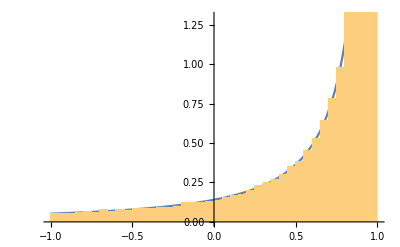

```mathematica
g=0.7;
Show[
Plot[2 Pi pHG[u,g],{u,-1,1}],
Histogram[Map[-((-1+g)^2+2 # (-1+g) (1+g^2)-2 #^2 (g+g^3))/(1+(-1+2 #) g)^2&,Table[RandomReal[],{i,1,100000}]],50,"PDF"]
]
Clear[b,g];
```

## Henyey-greenstein Scattering (Flatland)

### Definition:

```mathematica
pH2[θ_,g_]:=1/(2 Pi)(1-g^2)/(1+g^2-2 g Cos[θ]);
```

### Moments

```mathematica
Integrate[pH2[t,g]Cos[t],{t,-Pi,Pi},Assumptions->g>-1&&g<1&&g≠0&&n≥0]
```

g

```mathematica
Integrate[pH2[t,g]Cos[2 t],{t,-Pi,Pi},Assumptions->g>-1&&g<1&&g≠0&&n≥0]
```

g^2

```mathematica
Integrate[pH2[t,g]Cos[7 t],{t,-Pi,Pi},Assumptions->g>-1&&g<1&&g≠0&&n≥0]
```

g^7

### Sampling:

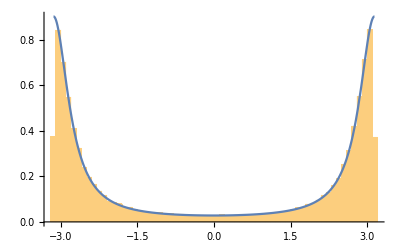

```mathematica
g=-0.7;
Show[
Histogram[Map[2 ArcTan[(1-g)/(1+g)Tan[Pi/2(1-2 #)]]&,Table[RandomReal[],{i,1,100000}]],50,"PDF"],Plot[ pH2[θ,g],{θ,-Pi,Pi},PlotRange->All]
]
Clear[g];
```

## Ellipsoidal Scattering

```mathematica
pEllipsoidal[u_,b_]:=b(2 Pi Log[(1+b)/(1-b)](1-b u))^-1
```

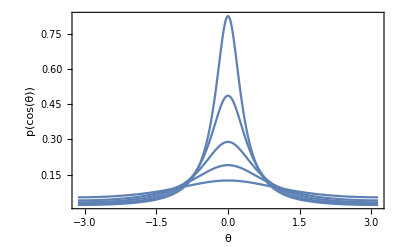

```mathematica
pEllplot=Show[
Plot[pEllipsoidal[Cos[t],.9],{t,-Pi,Pi},PlotRange->All],
Plot[pEllipsoidal[Cos[t],.8],{t,-Pi,Pi},PlotRange->All],
Plot[pEllipsoidal[Cos[t],.65],{t,-Pi,Pi},PlotRange->All],
Plot[pEllipsoidal[Cos[t],.4],{t,-Pi,Pi},PlotRange->All],
Plot[pEllipsoidal[Cos[t],.95],{t,-Pi,Pi},PlotRange->All],
Frame->True,
ImageSize->400,
FrameLabel->{{p[Cos[θ]],},{θ,"Ellipsoidal Scattering, b = 0.4, 0.65, 0.8, 0.9, 0.95"}}]
```

### sampling

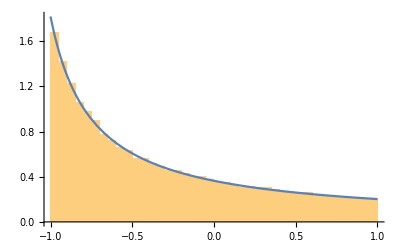

```mathematica
b=-0.8;
Show[Histogram[Map[(1-(1+b) ((1+b)/(1-b))^-#)/b&,Table[RandomReal[],{i,1,100000}]],50,"PDF"],
Plot[2 Pi pEllipsoidal[u,b],{u,-1,1}]

]
Clear[b];
```

## Binomial Scattering

```mathematica
pBinomial[u_,n_]:=Pi^-1((n+1)/2^(n+2))(1+u)^n
```

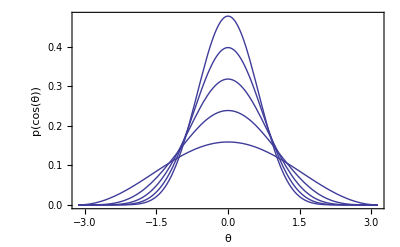

```mathematica
pBinplot=Show[
Plot[pBinomial[Cos[t],1],{t,-Pi,Pi},PlotRange->All],
Plot[pBinomial[Cos[t],2],{t,-Pi,Pi},PlotRange->All],
Plot[pBinomial[Cos[t],3],{t,-Pi,Pi},PlotRange->All],
Plot[pBinomial[Cos[t],4],{t,-Pi,Pi},PlotRange->All],
Plot[pBinomial[Cos[t],5],{t,-Pi,Pi},PlotRange->All],
Frame->True,
ImageSize->400,
FrameLabel->{{p[Cos[θ]],},{θ,"Binomial Scattering, n = 1, 2, 3, 4, 5"}}]
```

### Normalization condition

```mathematica
Integrate[2 Pi pBinomial[u,n],{u,-1,1},Assumptions->n≥0]
```

1

### Mean cosine (g)

```mathematica
Integrate[2 Pi pBinomial[u,n]u,{u,-1,1},Assumptions->n≥0]
```

n/(2+n)

### sampling

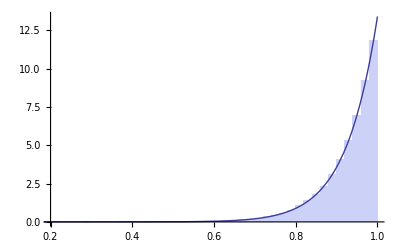

```mathematica
n=25.8;
Show[Histogram[Map[-1+(2^(1+n) #)^(1/(1+n))&,Table[RandomReal[],{i,1,100000}]],50,"PDF"],
Plot[2 Pi pBinomial[u,n],{u,-1,1},PlotRange->All]

]
Clear[b];
```

## Liu Scattering

```mathematica
pLiu[u_,e_,m_]:=(e(2m+1)(1+e u)^(2m))/(2 Pi((1+e)^(2m+1)-(1-e)^(2m+1)))
```

```mathematica
Clear[m]
```

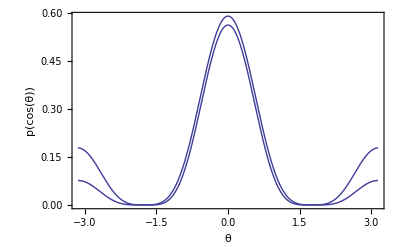

```mathematica
pLiuplot=Show[
Plot[pLiu[Cos[t],4,2],{t,-Pi,Pi},PlotRange->All],
Plot[pLiu[Cos[t],7,2],{t,-Pi,Pi},PlotRange->All],
Frame->True,
ImageSize->400,
FrameLabel->{{p[Cos[θ]],},{θ,"Liu Scattering, (m = 2, ϵ = 4), (m = 2, ϵ = 7)"}}]
```

### Normalization condition

```mathematica
Integrate[2 Pi pLiu[u,e,m],{u,-1,1},Assumptions->e>0&&m>0&&m∈Integers]
```

1

### Mean cosine (g)

```mathematica
Integrate[2 Pi u pLiu[u,e,m],{u,-1,1},Assumptions->e>0&&m>0&&m∈Integers&&e<1]
```

((1+e)^(1+2 m) (-1+e+2 e m)+(1-e)^(1+2 m) (1+e+2 e m))/(2 e (-(1-e)^(1+2 m)+(1+e)^(1+2 m)) (1+m))

### Legendre expansion coefficients

```mathematica
Integrate[2Pi(2k+1) pLiu[u,e,m]LegendreP[k,u]/.k->0,{u,-1,1},Assumptions->m>0&&m∈Integers&&e∈Reals&&e≠0&&Abs[e]<1]
```

1

```mathematica
Integrate[2Pi(2k+1) pLiu[u,e,m]LegendreP[k,u]/.k->2,{u,-1,1},Assumptions->m>0&&m∈Integers&&e∈Reals&&e≠0&&Abs[e]<1]
```

(5 ((1+e)^(1+2 m) (3+e (-3+2 m (-3+2 e (1+m))))+(1-e)^(2 m) (-1+e) (3+e (3+2 m (3+2 e (1+m))))))/(2 e^2 (-(1-e)^(1+2 m)+(1+e)^(1+2 m)) (1+m) (3+2 m))

### sampling

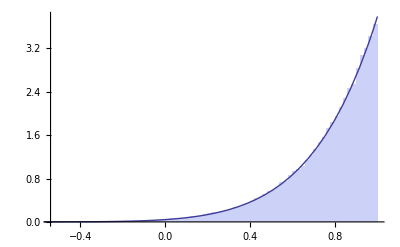

```mathematica
m=3.5;
ϵ=0.9;
Show[Histogram[Map[(-1+((-1+#) (1-ϵ)^(2 m) (-1+ϵ)+# (1+ϵ)^(1+2 m))^(1/(1+2 m)))/ϵ&,Table[RandomReal[],{i,1,100000}]],50,"PDF"],
Plot[2 Pi pLiu[u,ϵ,m],{u,-1,1},PlotRange->All]

]
Clear[m,ϵ];
```

## Gegenbauer Scattering

```mathematica
pGegenbauer[u_,g_,a_]:=((1 + g^2-2 g u)^(-(a+1)))/((((1-g)^(-2 a)-(1+g)^(-2 a)) π)/(a g))
```

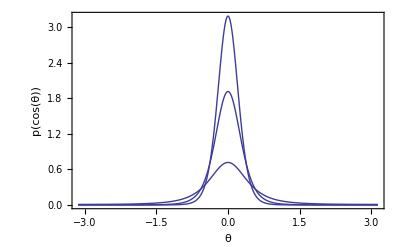

```mathematica
Show[
Plot[pGegenbauer[Cos[t],0.5,1],{t,-Pi,Pi},PlotRange->All],
Plot[pGegenbauer[Cos[t],0.5,3],{t,-Pi,Pi},PlotRange->All],
Plot[pGegenbauer[Cos[t],0.5,5],{t,-Pi,Pi},PlotRange->All],

Frame->True,
FrameLabel->{{p[Cos[θ]],},{θ,"Gegenbauer Scattering, G = 0.5, a = 1, 3, 5"}}]
```

### Normalization condition

```mathematica
Integrate[2 Pi pGegenbauer[u,g,a],{u,-1,1},Assumptions->-1≤g≤1&&a>0]
```

1

### Mean cosine (g)

```mathematica
Integrate[2 Pi u pGegenbauer[u,g,a],{u,-1,1},Assumptions->-1≤g≤1&&a>0]
```

((1+g)^(2 a) (1-2 a g+g^2)-(1-g)^(2 a) (1+2 a g+g^2))/(2 (-1+a) g ((1-g)^(2 a)-(1+g)^(2 a)))

### Legendre expansion coefficients

```mathematica
Integrate[2Pi(2k+1) pGegenbauer[u,g,a]LegendreP[k,u]/.k->0,{u,-1,1},Assumptions->-1≤g≤1&&a>0]
```

1

```mathematica
FullSimplify[Integrate[2Pi(2k+1) pGegenbauer[u,g,a]LegendreP[k,u]/.k->3,{u,-1,1},Assumptions->-1≤g≤1&&a>0]]
```

-(7 (24 a^2 g^2 (1+g^2) ((1-g)^(2 a)-(1+g)^(2 a))+3 (5+3 g^2+3 g^4+5 g^6) ((1-g)^(2 a)-(1+g)^(2 a))+8 a^3 g^3 ((1-g)^(2 a)+(1+g)^(2 a))+2 a g (15+14 g^2+15 g^4) ((1-g)^(2 a)+(1+g)^(2 a))))/(8 (-3+a) (-2+a) (-1+a) g^3 ((1-g)^(2 a)-(1+g)^(2 a)))

### sampling

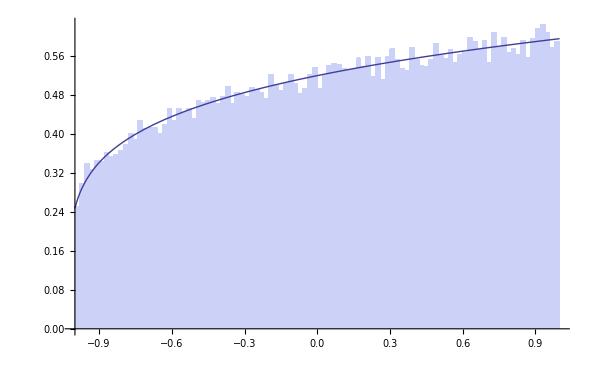

```mathematica
g=-0.8;
a=-1.2;
Show[Histogram[Map[(1+g^2-(# (1-g)^(-2 a)-(-1+#) (1+g)^(-2 a))^(-1/a))/(2 g)&,Table[RandomReal[],{i,1,100000}]],100,"PDF"],
Plot[2 Pi pGegenbauer[u,g,a],{u,-1,1},PlotRange->All]

]
Clear[g,a];
```

## vMF (spherical Gaussian) Scattering

```mathematica
pVMF[u_,k_]:=k/(4Pi  Sinh[k])Exp[k u]
```

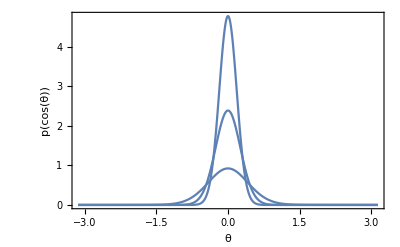

```mathematica
Show[
Plot[pVMF[Cos[t],5.8],{t,-Pi,Pi},PlotRange->All],
Plot[pVMF[Cos[t],15],{t,-Pi,Pi},PlotRange->All],
Plot[pVMF[Cos[t],30],{t,-Pi,Pi},PlotRange->All],

Frame->True,
FrameLabel->{{p[Cos[θ]],},{θ,"vMF, k = {5.8,15,30}"}}]
```

### Normalization condition

```mathematica
Integrate[2 Pi pVMF[u,k],{u,-1,1},Assumptions->k>0]
```

1

### Mean cosine (g)

```mathematica
Integrate[2 Pi u pVMF[u,k],{u,-1,1},Assumptions->k>0]
```

-1/k+Coth[k]

### Legendre expansion coefficients

```mathematica
Integrate[2Pi(2o+1)pVMF[u,k]LegendreP[o,u]/.o->4,{u,-1,1},Assumptions->k>0]
```

(9 (105+45 k^2+k^4-5 k (21+2 k^2) Coth[k]))/k^4

### sampling

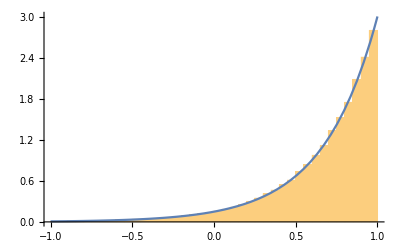

```mathematica
k=3;
Show[Histogram[Map[Log[E^-k(1-#)+E^k#]/k&,Table[RandomReal[],{i,1,100000}]],50,"PDF"],
Plot[2 Pi pVMF[u,k],{u,-1,1},PlotRange->All]

]
Clear[k];
```